## Forced Extra Coupling in Three Resonators

```mathematica
k1=.
k2=.
k3=.
k4=.
wd=.
g=.
k5=.
F=.
m1=.
m2=.
m3=.
DefaultTicksStylepaclet:ref/DefaultTicksStyle-> Directive[Black,FontSize->20];
DefaultAxesStyle->Directive[Black,FontSize->20];
```

1.) Start with equations of motion

x1[t]'' + g1*x1[t]’ + (k1/m1)*x1[t] + (k2/m1)*(x1[t] - x2[t]) == F*Cos[w*t]/m1;
x2[t]'' + g2*x2[t]’ + (k5/m2)*x2[t] + (k2/m2)*(x2[t] - x1[t]) + (k3/m2)*(x2[t] - x3[t]) == 0;
x3[t]'' + g3*x3[t]’ + (k4/m3)*x3[t] + (k3/m3)*(x3[t] - x2[t]) == 0;

2.) Solve steady state solution (same as above but drop forcing term to find homogeneous solution)

x1[t]'' + g1*x1[t]’ + (k1/m1)*x1[t] + (k2/m1)*(x1[t] - x2[t]) == 0;
x2[t]'' + g2*x2[t]’ + (k5/m2)*x2[t] + (k2/m2)*(x2[t] - x1[t]) + (k3/m2)*(x2[t] - x3[t]) = 0;
x3[t]'' + g3*x3[t]’ + (k4/m3)*x3[t] + (k3/m3)*(x3[t] - x2[t]) == 0;

Note that when solving for “Damped Coupled Resonators” it still held that the eigenvalues of the damped steady state solution were equal to w1^2-g^2/4 and w2^2-g^2/4. Also note that adding damping did not affect the eigenvector values at all.Therefore, I will assume that this holds for the case of three damped resonators as well, and solve for the eigenvalues and eigenfrequencies as in “Extre Coupling in Three Resonators” without damping terms.

Guess an exponential solution. Plug into diff eq and cross out exponentials. Then left with A, B, and C.

3.) Organize into matrix form such that M*{A,B,C}=w^2*{A,B,C}

```mathematica
M={{(k1/m1)+(k2/m1),-k2/m1,0},{-k2/m2,(k5/m2)+(k2/m2)+(k3/m2),-k3/m2},{0,-k3/m3,(k4/m3)+(k3/m3)}};
```

```mathematica
MatrixForm[M]
```

(k1/m1+k2/m1 | -k2/m1 | 0
-k2/m2 | k2/m2+k3/m2+k5/m2 | -k3/m2
0 | -k3/m3 | k3/m3+k4/m3)

Verify :

```mathematica
ddx1 + (k1/m1)*x1 + (k2/m1)*(x1- x2)
```

ddx1+(k1 x1)/m1+(k2 (x1-x2))/m1

```mathematica
(M.{ddx1,ddx2,ddx3})[[1]]
```

ddx1 (k1/m1+k2/m1)-(ddx2 k2)/m1

```mathematica
ddx1 + (k1/m1)*x1 + (k2/m1)*(x1- x2)  == (M.{ddx1,ddx2,ddx3})[[1]]
```

ddx1+(k1 x1)/m1+(k2 (x1-x2))/m1==ddx1 (k1/m1+k2/m1)-(ddx2 k2)/m1

```mathematica
M.{ddx1,ddx2,ddx3} + {k1,k2,k3}.{x1,x2,x3}
```

{ddx1 (k1/m1+k2/m1)-(ddx2 k2)/m1+k1 x1+k2 x2+k3 x3,ddx2 (k2/m2+k3/m2+k5/m2)-(ddx1 k2)/m2-(ddx3 k3)/m2+k1 x1+k2 x2+k3 x3,ddx3 (k3/m3+k4/m3)-(ddx2 k3)/m3+k1 x1+k2 x2+k3 x3}

5.) Find Eigenvectors of matrix to and set them equal to A, B, and C values

```mathematica
{{A1,B1,C1},{A2,B2,C2},{A3,B3,C3}}=Eigenvectors[M];
```

6.) Find Eigenvalues of matrix and set them equal to e1, e2, e3

```mathematica
{e1,e2,e3}=Eigenvalues[M];
```

7.) Solve for w1, w2, and w3

```mathematica
{w1,w2,w3}={Sqrt[e1-g^2/4],Sqrt[e2-g^2/4],Sqrt[e3-g^2/4]};
```

Can also write w values as functions to plot avoided crossings later

```mathematica
w11[k3_]:=Sqrt[e1]
w22[k3_]:=Sqrt[e2]
w33[k3_]:=Sqrt[e3]
```

Note that these solutions have the form x1[t]=A*e^-g*t/2*Cos[w*t]

8.) Solve for non-homogeneous solution by guessing solution term that oscillates as x[t]=D*e^[i*wd*t + d] and write force as a complex exponential

-wd^2*D1 + I*wd*g*D1 + (k1/m)*D1 + (k2/m)*(D1 - D2) == F/m;
-wd^2*D2 + I*wd*g*D2 + (k5/m)*D2 + (k2/m)*(D2 - D1) + (k3/m)*(D2 - D3) == 0; -wd^2*D3 + I*wd*g*D3 + (k4/m)*D3 + (k3/m)*(D3 - D2) == 0;

9.) Write equations in matrix from such that M2*{D1,D2,D3}={F/m,0,0}

```mathematica
M2 = {{-wd^2+I*wd*g+(k1/m1)+(k2/m1),-k2/m1,0},{-k2/m2,-wd^2+I*wd*g+(k5/m2)+(k2/m2)+(k3/m2),-k3/m2},{0,-k3/m3,-wd^2+I*wd*g+(k4/m3)+(k3/m3)}};
MatrixForm[M2]
```

(k1/m1+k2/m1+ⅈ g wd-wd^2 | -k2/m1 | 0
-k2/m2 | k2/m2+k3/m2+k5/m2+ⅈ g wd-wd^2 | -k3/m2
0 | -k3/m3 | k3/m3+k4/m3+ⅈ g wd-wd^2)

10.) Write three matrices with force terms to use Cramer’s Rule

```mathematica
R1={{F/m1,-k2/m1,0},{0,-wd^2+I*wd*g+(k5/m2)+(k2/m2)+(k3/m2),-k3/m2},{0,-k3/m3,-wd^2+I*wd*g+(k4/m3)+(k3/m3)}};
R2={{-wd^2+I*wd*g+(k1/m1)+(k2/m1),F/m1,0},{-k2/m2,0,-k3/m2},{0,0,-wd^2+I*wd*g+(k4/m3)+(k3/m3)}};
R3={{-wd^2+I*wd*g+(k1/m1)+(k2/m1),-k2/m1,F/m1},{-k2/m2,-wd^2+I*wd*g+(k5/m2)+(k2/m2)+(k3/m2),0},{0,-k3/m3,0}};
MatrixForm[R1]
MatrixForm[R2]
MatrixForm[R3]
```

(F/m1 | -k2/m1 | 0
0 | k2/m2+k3/m2+k5/m2+ⅈ g wd-wd^2 | -k3/m2
0 | -k3/m3 | k3/m3+k4/m3+ⅈ g wd-wd^2)

(k1/m1+k2/m1+ⅈ g wd-wd^2 | F/m1 | 0
-k2/m2 | 0 | -k3/m2
0 | 0 | k3/m3+k4/m3+ⅈ g wd-wd^2)

(k1/m1+k2/m1+ⅈ g wd-wd^2 | -k2/m1 | F/m1
-k2/m2 | k2/m2+k3/m2+k5/m2+ⅈ g wd-wd^2 | 0
0 | -k3/m3 | 0)

11.) Solve for complex coefficients Do1, Do2, and Do3 using Cramer’s Rule

```mathematica
{Do1,Do2,Do3}={Det[R1]/Det[M2],Det[R2]/Det[M2],Det[R3]/Det[M2]};
```

12.) Complex expand coefficients so that we can solve for D and for delta term

```mathematica
{RDo1,IDo1}={ComplexExpand[Re[Do1]],ComplexExpand[Im[Do1]]};
{RDo2,IDo2}={ComplexExpand[Re[Do2]],ComplexExpand[Im[Do2]]};
{RDo3,IDo3}={ComplexExpand[Re[Do3]],ComplexExpand[Im[Do3]]};
```

13.) Solve for D coefficients (D1, D2, D3) and delta terms (d1, d2, d3)

```mathematica
{d1,d2,d3}={ArcTan[RDo1,IDo1],ArcTan[RDo2,IDo2],ArcTan[RDo3,IDo3]};
```

2120.83

-512.563

1198.5

-308.283

-3.40732

-121.388

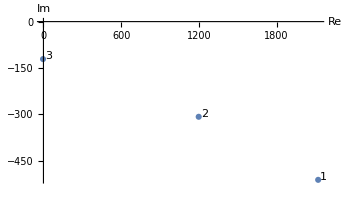

-13.5867

-14.4251

-91.6079

```mathematica
k1=1;
k2=1;
k3=0.01;
k4=1;
k5=1;
g=0.1;
F=1000;
 wd=w1-.01; (* driving near resonance *)
m1=1;
m2 = 1/4;
m3 =1;
RDo1
IDo1 
RDo2
IDo2
RDo3
IDo3
ListPlot[{Labeled[{RDo1,IDo1},1],Labeled[{RDo2,IDo2},2],Labeled[{RDo3,IDo3},3]}, AxesLabel-> {Re, Im}, AspectRatio->Automatic]
d1*180/Pi //N
d2*180/Pi //N
d3*180/Pi //N
Clear[k1,k2,k3,k4,k5,kg,F,m1,m2,m3]
```

```mathematica
{D1,D2,D3}={RDo1/Cos[d1],RDo2/Cos[d2],RDo3/Cos[d3]};

amp1[wd_] = D1;
amp2[wd_]=D2;
amp3[wd_] = D3;
```

```mathematica
x1solution := A1*Exp[-g*t/2]*Cos[w1*t]+A2*Exp[-g*t/2]*Cos[w2*t]+A3*Exp[-g*t/2]*Cos[w3*t]+D1*Cos[wd*t+d1]
x2solution :=B1*Exp[-g*t/2]*Cos[w1*t]+B2*Exp[-g*t/2]*Cos[w2*t]+B3*Exp[-g*t/2]*Cos[w3*t]+D2*Cos[wd*t+d2]
x3solution := C1*Exp[-g*t/2]*Cos[w1*t]+C2*Exp[-g*t/2]*Cos[w2*t]+C3*Exp[-g*t/2]*Cos[w3*t]+D3*Cos[wd*t+d3]
xsolutions = {x1solution,x2solution,x3solution};

x1longtime := D1*Cos[wd*t+d1];
x2longtime := D2*Cos[wd*t+d2];
x3longtime := D3*Cos[wd*t+d3];
xsolutionslongtime = {x1longtime,x2longtime,x3longtime};
```

```mathematica
(* the D1, D2, and D3 are the long-time amplitudes *)
(* d1, d2, d3 are the long-time phases *)
```

14.) Plot results

```mathematica
k1=1;
k2=1;
k3=0.01;
k4=1;
k5=1;
g=0.1;
F=1000;
(* wd:=w1-.01; *)(* driving near resonance *)
m1=1;
m2 = 1/4;
m3 =1.2;
maxwd = w3+w1;

(*Plot[xsolutionslongtime,{t,0,20},PlotLabels->{"x1","x2","x3"}, AxesLabel-> {t, "Position"}]
w1
w2
w3
D1 
D2 
D3
d1
d2
d3
Clear[wd]*)
wd =.
imagesize = 350;
imagepad = {{60,2},{1,1}};
Multicolumn[{Plot[{Log10[amp1[wd]^2],Log10[amp2[wd]^2],Log10[amp3[wd]^2]}, {wd, 0,maxwd}, PlotLabels->{"Log D1^2","Log D2^2","Log D3^2"},FrameLabel->{Null, "Log Square Amplitude"},FrameTicksStyle->Directive[Black,FontSize->12],FrameStyle->Directive[Black,FontSize->12], PlotLegends->"Expressions", Frame-> True, ImageSize->imagesize,ImagePadding->imagepad],
Plot[{d1, d2, d3}, {wd, 0, maxwd},PlotLabels->{"d1", "d2", "d3"},FrameLabel-> {Null, "Phase (rad)"},FrameTicks-> {Automatic,{-Pi, -Pi/2, 0, Pi/2, Pi}},FrameTicksStyle->Directive[Black,FontSize->12],FrameStyle->Directive[Black,FontSize->12], PlotLegends->"Expressions", Frame-> True, ImageSize->imagesize,ImagePadding->imagepad],
Plot[{(d2-d1), (d3-d1), d3-d2}, {wd, 0, maxwd},PlotRange-> Full, FrameStyle->Directive[Black,FontSize->12], PlotLabels->{"d2-d1", "d3-d1", "d3-d2"},FrameLabel-> {"Drive frequency", "Phase difference (rad)"},FrameTicks-> {Automatic,{-Pi, -Pi/2, 0, Pi/2, Pi, 3 Pi/2, 2 Pi}},FrameTicksStyle->Directive[Black,FontSize->12], PlotLegends->"Expressions",Frame-> True, ImageSize->imagesize,ImagePadding->imagepad]},1,Spacings->{0,0}]

Clear[k1,k2,k3,k4,k5,g,F,m1,m2,m3]
```

-Graphics-
-Graphics-
-Graphics-

(x1 in blue, x2 in orange, x3 in green)  (w1,w2, and w3 are the eigenvalues of the matrix, i.e. normal mode freqs. w1 is the mode in which they are all in phase.)

15.) Plot avoided crossings of w1, w2, and w3 as a function of k3

```mathematica
k1=1;
k2=1;
k4=1;
k5=1;
m1=1;
m2 = 1/4;
m3 = 1;

Plot[{w11[k3],w22[k3],w33[k3]},{k3,0,2},PlotRange-> {0,Automatic},PlotLabels->{"w1","w2","w3"}, AxesLabel-> {k3,"Resonance frequency"},AxesStyle->Directive[Black,FontSize->12]]
Clear[k1,k2,k4,m1,m2,m3]
```

-Graphics-